```mathematica
Exit[];
```

## Define static objects

```mathematica
(* Classical Hamiltonian potential *)
V=-Γ (Sin[Subscript[θ, 1][t]]+Sin[Subscript[θ, 2][t]]+Sin[Subscript[θ, 3][t]])+h1 Cos[Subscript[θ, 1][t]]+h2 Cos[Subscript[θ, 2][t]]+h3 Cos[Subscript[θ, 3][t]]+J(Cos[Subscript[θ, 1][t]]Cos[Subscript[θ, 2][t]]+Cos[Subscript[θ, 1][t]]Cos[Subscript[θ, 3][t]]+Cos[Subscript[θ, 2][t]]Cos[Subscript[θ, 3][t]]);
(* Quantum Hamiltonian *)
sx = PauliMatrix[1];sz=PauliMatrix[3];id2=PauliMatrix[0];sy=PauliMatrix[2];
sx1 = KroneckerProduct[sx, id2, id2]; sx2 = KroneckerProduct[id2, sx, id2]; sx3 = KroneckerProduct[id2, id2, sx];
sz1 = KroneckerProduct[sz, id2, id2];sz2 = KroneckerProduct[id2, sz, id2];sz3 = KroneckerProduct[id2, id2, sz];
sy1 = KroneckerProduct[sy, id2, id2];sy2 = KroneckerProduct[id2, sy, id2];sy3 = KroneckerProduct[id2, id2, sy];
H =-Γ(sx1 + sx2 + sx3)/2 + J(sz1.sz2+sz1.sz3+sz2.sz3)/4 + (h1 sz1 + h2 sz2 + h3 sz3)/2;
(* The ψ operator*)
ψop = (sz1 + sz2 Exp[2π ⅈ / 3]+sz3 Exp[4π  ⅈ / 3]);
(* init states *)
z= {1, 0}; 
o = {0, 1};
```

## Define solvers and state preparation functions

```mathematica
genInitAngles[stateStr_]:=Module[{initAngles, chars},
initAngles = {};
chars = Characters[stateStr];
Table[If[chars[[i]]=="u", AppendTo[initAngles, Subscript[θ, i][0]==0],AppendTo[initAngles, Subscript[θ, i][0]==π]], {i, 1, Length[chars]}];

Return[initAngles];
];
solveClassical[params_, initAngles_, tf_, dt_:0.1]:=Module[{eqs, initDer,angles},
eqs = Table[D[Subscript[θ, i][t], {t,2}] - D[V, Subscript[θ, i][t]]==0, {i, 1, 3}]/.params;
initDer = Table[Subscript[θ, i]'[0]==0,{i,1,3}];
angles = NDSolveValue[Join[eqs, initAngles, initDer], {Subscript[θ, 1], Subscript[θ, 2], Subscript[θ, 3]}, {t, 0, tf}];

Return[angles];
];
getClassicalPsi[angles_,tf_,dt_]:=Module[{ψ, times, ψtimes},
ψ =  Cos[angles[[1]][t]] + Cos[angles[[2]][t]] Exp[2 π ⅈ / 3] + Cos[angles[[3]][t]] Exp[4 π ⅈ /3];
times = Table[tp, {tp, 0, tf, dt}];
ψtimes = Table[ψ/.{t->times[[i]]}, {i, 1, Length[times]}];

Return[ψtimes];
];
genInitState[stateStr_]:=Module[{stateList,chars, initState},
stateList = {};
chars = Characters[stateStr];
Table[If[chars[[i]]=="u", AppendTo[stateList,{1,0}],AppendTo[stateList, {0,1}]], {i, 1, Length[chars]}];
initState = Flatten[KroneckerProduct@@stateList];

Return[initState];
];
solveSchrodinger[params_,initState_,tf_, dt_:0.1]:=Module[{phi, phiSol,times,phit, ψtimes},
phi[t_] = Table[Subscript[ϕ, i][t],{i, 1, 8}];
phiSol = NDSolveValue[{phi'[t]+ⅈ (H/.params).phi[t]==ConstantArray[0, 8], phi[0]==initState}, phi[t], {t, 0, tf}];

Return[phiSol]
];
getSchrodingerZExpVals[phiSol_,tf_,dt_]:=Module[{times, phit, z1t, z2t, z3t},
times = Table[tp, {tp, 0, tf, dt}];
phit = Table[phiSol/.{t->times[[i]]}, {i, 1, Length[times]}];
z1t = Table[ConjugateTranspose[phit[[i]]].sz1.phit[[i]]//Re, {i, 1, Length[times]}];
z2t = Table[ConjugateTranspose[phit[[i]]].sz2.phit[[i]]//Re, {i, 1, Length[times]}];
z3t = Table[ConjugateTranspose[phit[[i]]].sz3.phit[[i]]//Re, {i, 1, Length[times]}];

Return[{z1t, z2t, z3t}]
];

getSchrodingerEntanglementEntropy[phiSol_, tf_, dt_]:=Module[{times, phit, rhot, a0, a1, rhoBCt,evals, entropy},
times = Table[tp, {tp, 0, tf, dt}];
phit = Table[phiSol/.{t->times[[i]]}, {i, 1, Length[times]}];
rhot = Table[KroneckerProduct[phit[[i]], ConjugateTranspose[phit[[i]]]], {i, 1, Length[times]}];
a0 = KroneckerProduct[{1, 0}, id2, id2]; a1 = KroneckerProduct[{0, 1}, id2, id2];
rhoBCt = Table[ConjugateTranspose[a0].rhot[[i]].a0 + ConjugateTranspose[a1].rhot[[i]].a1, {i, 1, Length[times]}];
evals = Table[Chop[Re[Eigenvalues[rhoBCt[[i]]]], 10^-8], {i, 1, Length[times]}];
entropy=Table[Re[Total[If[#==0,0.,-#*Log[#]]&/@evals[[i]]]], {i, 1, Length[times]}];

Return[entropy];
];

getSchrodingerPsi[phiSol_,tf_,dt_]:=Module[{times, phit, ψtimes},
times = Table[tp, {tp, 0, tf, dt}];
phit = Table[phiSol/.{t->times[[i]]}, {i, 1, Length[times]}];
ψtimes = Table[ConjugateTranspose[phit[[i]]].ψop.phit[[i]], {i, 1, Length[times]}];

Return[ψtimes]
];

solveLindblad[params_,initState_,tf_,γ_, dt_:0.1]:=Module[{phi, phiSol,times,phit, ψtimes},
rho[t_]:=Table[Subscript[ρ, i,j][t], {i, 1, 8}, {j, 1, 8}];
rhoInit = KroneckerProduct[initState, Conjugate[initState]];
rhoLindSol = NDSolveValue[{Flatten[rho'[t]+ⅈ((H.rho[t]-rho[t].H)/.params)-γ(sz1.rho[t].sz1-rho[t])-γ(sz2.rho[t].sz2-rho[t])-γ(sz3.rho[t].sz3-rho[t])]==ConstantArray[0,4], rho[0]==rhoInit},rho[t], {t, 0, tf}];
phiSol = NDSolveValue[{phi'[t]+ⅈ (H/.params).phi[t]==ConstantArray[0, 8], phi[0]==initState}, phi[t], {t, 0, tf}];

Return[phiSol]
];
```

### Input state |110>

```mathematica
(* Set up parameters for solvers *)
params = {J->0,Γ->1, h1->0,h2->0,h3->0};
stateStr = "ddu";
initAngles = genInitAngles[stateStr];
initState =genInitState[stateStr];
tf = 20;
dt = 1/10;

(* Actually solve in both cases *)
classSol = solveClassical[params,initAngles,tf];
classPsi = getClassicalPsi[classSol, tf, dt];
quantumSol = solveQuantum[params,initState,tf];
quantumPsi = getQuantumPsi[quantumSol, tf, dt];

(* Generate all types of plot data we would like to compare *)
times = Table[t, {t, 0, tf, dt}];
(* Classical data *)
classPsiData = Table[{times[[i]], classPsi[[i]]}, {i, 1, Length[times]}];
theta1Data = Table[{t, classSol[[1]][t]}, {t, times}];
cosTheta1Data = Table[{t, Cos[classSol[[1]][t]]}, {t, times}];
theta2Data = Table[{t, classSol[[2]][t]}, {t, times}];
cosTheta2Data = Table[{t, Cos[classSol[[2]][t]]}, {t, times}];
theta3Data = Table[{t, classSol[[3]][t]}, {t, times}];
cosTheta3Data = Table[{t, Cos[classSol[[3]][t]]}, {t, times}];
(* Unitary Quantum Data *)
quantumPsiData = Table[{times[[i]], quantumPsi[[i]]}, {i, 1, Length[times]}];
{z1t, z2t, z3t} = getQuantumZExpVals[quantumSol, tf, dt];
z1Data = Table[{times[[i]], z1t[[i]]}, {i, 1, Length[times]}];
z2Data = Table[{times[[i]], z2t[[i]]}, {i, 1, Length[times]}];
z3Data = Table[{times[[i]], z3t[[i]]}, {i, 1, Length[times]}];
rawEntropy = getQuantumEntanglementEntropy[quantumSol, tf, dt];
entropyData = Table[{times[[i]], rawEntropy[[i]]}, {i, 1, Length[times]}];
```

```mathematica
plt = ListPlot[{cosTheta1Data, z1Data},AxesLabel->{"time", "Z expectation value"}, PlotLegends->{"Classical", "Schrodinger"}, PlotLabel->"J = 0, Γ = 1, Using (σz/2)'s in H", PlotLabels->{"C", "S"}]
```

-Graphics-

```mathematica
cosTheta1Data
```

{{0,Cos[3.14159[0]]},{1/10,Cos[3.13659[1/10]]},{1/5,Cos[3.12159[1/5]]},{3/10,Cos[3.0966[3/10]]},{2/5,Cos[3.06161[2/5]]},{1/2,Cos[3.01666[1/2]]},{3/5,Cos[2.96179[3/5]]},{7/10,Cos[2.89708[7/10]]},{4/5,Cos[2.82268[4/5]]},{9/10,Cos[2.73879[9/10]]},{1,Cos[2.64571[1]]},{11/10,Cos[2.54384[11/10]]},{6/5,Cos[2.43372[6/5]]},{13/10,Cos[2.31602[13/10]]},{7/5,Cos[2.19154[7/5]]},{3/2,Cos[2.06126[3/2]]},{8/5,Cos[1.92628[8/5]]},{17/10,Cos[1.78783[17/10]]},{9/5,Cos[1.64723[9/5]]},{19/10,Cos[1.50587[19/10]]},{2,Cos[1.36516[2]]},{21/10,Cos[1.22648[21/10]]},{11/5,Cos[1.09117[11/5]]},{23/10,Cos[0.960465[23/10]]},{12/5,Cos[0.835479[12/5]]},{5/2,Cos[0.71719[5/2]]},{13/5,Cos[0.606424[13/5]]},{27/10,Cos[0.503864[27/10]]},{14/5,Cos[0.41005[14/5]]},{29/10,Cos[0.325398[29/10]]},{3,Cos[0.250214[3]]},{31/10,Cos[0.184712[31/10]]},{16/5,Cos[0.129036[16/5]]},{33/10,Cos[0.0832736[33/10]]},{17/5,Cos[0.0474744[17/5]]},{7/2,Cos[0.0216627[7/2]]},{18/5,Cos[0.00584806[18/5]]},{37/10,Cos[0.0000331214[37/10]]},{19/5,Cos[0.00421818[19/5]]},{39/10,Cos[0.018403[39/10]]},{4,Cos[0.0425857[4]]},{41/10,Cos[0.0767583[41/10]]},{21/5,Cos[0.120899[21/5]]},{43/10,Cos[0.174965[43/10]]},{22/5,Cos[0.238873[22/5]]},{9/2,Cos[0.312491[9/2]]},{23/5,Cos[0.395618[23/5]]},{47/10,Cos[0.487964[47/10]]},{24/5,Cos[0.589132[24/5]]},{49/10,Cos[0.698603[49/10]]},{5,Cos[0.815719[5]]},{51/10,Cos[0.939676[51/10]]},{26/5,Cos[1.06952[26/5]]},{53/10,Cos[1.20416[53/10]]},{27/5,Cos[1.34238[27/5]]},{11/2,Cos[1.48285[11/2]]},{28/5,Cos[1.62421[28/5]]},{57/10,Cos[1.76503[57/10]]},{29/5,Cos[1.90392[29/5]]},{59/10,Cos[2.03955[59/10]]},{6,Cos[2.17068[6]]},{61/10,Cos[2.29617[61/10]]},{31/5,Cos[2.41503[31/5]]},{63/10,Cos[2.52644[63/10]]},{32/5,Cos[2.62969[32/5]]},{13/2,Cos[2.72424[13/2]]},{33/5,Cos[2.80965[33/5]]},{67/10,Cos[2.88561[67/10]]},{34/5,Cos[2.95191[34/5]]},{69/10,Cos[3.00839[69/10]]},{7,Cos[3.05496[7]]},{71/10,Cos[3.09157[71/10]]},{36/5,Cos[3.1182[36/5]]},{73/10,Cos[3.13483[73/10]]},{37/5,Cos[3.14146[37/5]]},{15/2,Cos[3.13809[15/2]]},{38/5,Cos[3.12472[38/5]]},{77/10,Cos[3.10135[77/10]]},{39/5,Cos[3.06799[39/5]]},{79/10,Cos[3.02466[79/10]]},{8,Cos[2.9714[8]]},{81/10,Cos[2.90829[81/10]]},{41/5,Cos[2.83546[41/5]]},{83/10,Cos[2.7531[83/10]]},{42/5,Cos[2.66149[42/5]]},{17/2,Cos[2.56102[17/2]]},{43/5,Cos[2.45221[43/5]]},{87/10,Cos[2.33569[87/10]]},{44/5,Cos[2.21225[44/5]]},{89/10,Cos[2.08285[89/10]]},{9,Cos[1.94855[9]]},{91/10,Cos[1.81058[91/10]]},{46/5,Cos[1.67024[46/5]]},{93/10,Cos[1.5289[93/10]]},{47/5,Cos[1.38799[47/5]]},{19/2,Cos[1.24889[19/2]]},{48/5,Cos[1.11294[48/5]]},{97/10,Cos[0.981406[97/10]]},{49/5,Cos[0.855418[49/5]]},{99/10,Cos[0.735976[99/10]]},{10,Cos[0.623934[10]]},{101/10,Cos[0.519996[101/10]]},{51/5,Cos[0.424725[51/5]]},{103/10,Cos[0.338556[103/10]]},{52/5,Cos[0.261812[52/5]]},{21/2,Cos[0.194721[21/2]]},{53/5,Cos[0.137436[53/5]]},{107/10,Cos[0.0900536[107/10]]},{54/5,Cos[0.0526282[54/5]]},{109/10,Cos[0.0251877[109/10]]},{11,Cos[0.00774341[11]]},{111/10,Cos[0.0002986[111/10]]},{56/5,Cos[0.00285377[56/5]]},{113/10,Cos[0.0154088[113/10]]},{57/5,Cos[0.0379623[57/5]]},{23/2,Cos[0.0705076[23/2]]},{58/5,Cos[0.113026[58/5]]},{117/10,Cos[0.165478[117/10]]},{59/5,Cos[0.22779[59/5]]},{119/10,Cos[0.299837[119/10]]},{12,Cos[0.381432[12]]},{121/10,Cos[0.472299[121/10]]},{61/5,Cos[0.572061[61/5]]},{123/10,Cos[0.68022[123/10]]},{62/5,Cos[0.796141[62/5]]},{25/2,Cos[0.919044[25/2]]},{63/5,Cos[1.048[63/5]]},{127/10,Cos[1.18194[127/10]]},{64/5,Cos[1.31966[64/5]]},{129/10,Cos[1.45986[129/10]]},{13,Cos[1.60117[13]]},{131/10,Cos[1.74217[131/10]]},{66/5,Cos[1.88147[66/5]]},{133/10,Cos[2.01772[133/10]]},{67/5,Cos[2.14966[67/5]]},{27/2,Cos[2.27614[27/2]]},{68/5,Cos[2.39615[68/5]]},{137/10,Cos[2.50882[137/10]]},{69/5,Cos[2.61344[69/5]]},{139/10,Cos[2.70944[139/10]]},{14,Cos[2.79636[14]]},{141/10,Cos[2.87388[141/10]]},{71/5,Cos[2.94177[71/5]]},{143/10,Cos[2.99986[143/10]]},{72/5,Cos[3.04805[72/5]]},{29/2,Cos[3.08629[29/2]]},{73/5,Cos[3.11454[73/5]]},{147/10,Cos[3.1328[147/10]]},{74/5,Cos[3.14106[74/5]]},{149/10,Cos[3.13932[149/10]]},{15,Cos[3.12758[15]]},{151/10,Cos[3.10584[151/10]]},{76/5,Cos[3.07411[76/5]]},{153/10,Cos[3.0324[153/10]]},{77/5,Cos[2.98076[77/5]]},{31/2,Cos[2.91925[31/2]]},{78/5,Cos[2.84799[78/5]]},{157/10,Cos[2.76716[157/10]]},{79/5,Cos[2.67704[79/5]]},{159/10,Cos[2.57798[159/10]]},{16,Cos[2.47049[16]]},{161/10,Cos[2.35517[161/10]]},{81/5,Cos[2.2328[81/5]]},{163/10,Cos[2.1043[163/10]]},{82/5,Cos[1.97073[82/5]]},{33/2,Cos[1.83327[33/2]]},{83/5,Cos[1.69322[83/5]]},{167/10,Cos[1.55195[167/10]]},{84/5,Cos[1.41087[84/5]]},{169/10,Cos[1.27138[169/10]]},{17,Cos[1.13483[17]]},{171/10,Cos[1.00249[171/10]]},{86/5,Cos[0.875531[86/5]]},{173/10,Cos[0.75496[173/10]]},{87/5,Cos[0.64166[87/5]]},{35/2,Cos[0.536359[35/2]]},{88/5,Cos[0.439642[88/5]]},{177/10,Cos[0.351965[177/10]]},{89/5,Cos[0.273667[89/5]]},{179/10,Cos[0.20499[179/10]]},{18,Cos[0.146099[18]]},{181/10,Cos[0.0970982[181/10]]},{91/5,Cos[0.0580475[91/5]]},{183/10,Cos[0.0289785[183/10]]},{92/5,Cos[0.00990453[92/5]]},{37/2,Cos[0.000829832[37/2]]},{93/5,Cos[0.00175511[93/5]]},{187/10,Cos[0.0126803[187/10]]},{94/5,Cos[0.0336044[94/5]]},{189/10,Cos[0.064522[189/10]]},{19,Cos[0.105417[19]]},{191/10,Cos[0.156254[191/10]]},{96/5,Cos[0.216966[96/5]]},{193/10,Cos[0.287437[193/10]]},{97/5,Cos[0.367492[97/5]]},{39/2,Cos[0.45687[39/2]]},{98/5,Cos[0.555213[98/5]]},{197/10,Cos[0.662043[197/10]]},{99/5,Cos[0.776748[99/5]]},{199/10,Cos[0.898572[199/10]]},{20,Cos[1.02661[20]]}}

```mathematica
Export["/Users/worknic/Programming/spinTransportOnDwave/analytical_calculations/using2Factor.nb", plt]
```

/Users/worknic/Programming/spinTransportOnDwave/analytical_calculations/using2Factor.nb

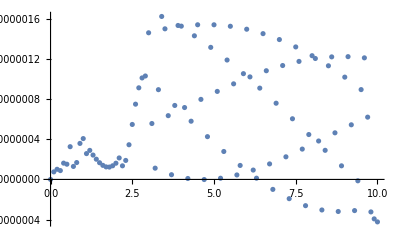

```mathematica
ListPlot[entropyData]
```

```mathematica
Plot[{(classSol[[1]][t])/π, (classSol[[2]][t])/π, (classSol[[3]][t])/π}, {t, 0, 10}, PlotLegends->{"θ_1", "θ_2", "θ_3"}, PlotLabels->{"θ_1", "θ_2", "θ_3"}]
```

-Graphics-

```mathematica
{z1t, z2t, z3t} = getQuantumZExpVals[quantumSol, tf, dt];
```

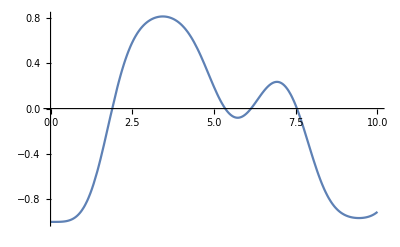

```mathematica
Plot[Cos[classSol[[1]][t]], {t, 0, 10}]
```

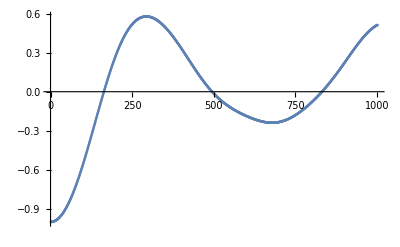

```mathematica
ListPlot[z1t]
```

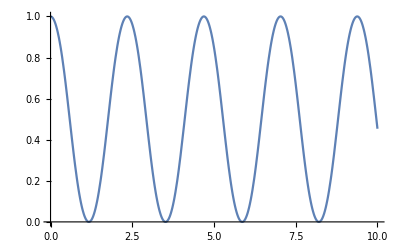

```mathematica
Plot[(classSol[[1]][t])/π, {t, 0, 10}]
```

```mathematica
data = Table[{t, (classSol[[1]][t])/π}, {t, 0, 10, 0.1}];
```

```mathematica
nlm =NonlinearModelFit[data, (Cos[ω t]+1)/2, ω, t]
```

FittedModel[1/2 (1+Cos[1.2251 t])]

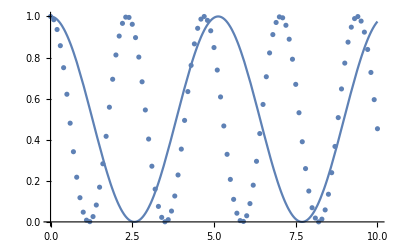

```mathematica
Show[ListPlot[data],Plot[nlm[t], {t, 0, 10}]]
```

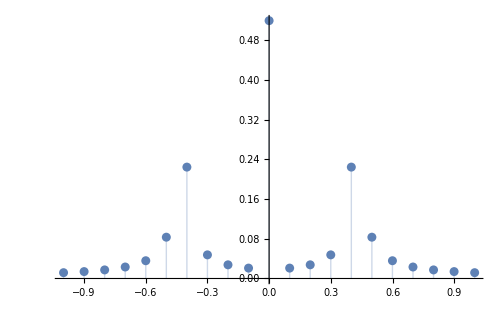

```mathematica
dt=10/1000;
els=Table[(classSol[[1]][t])/π,{t,0.,10,dt}];
n=Length[els];
(*ssf=RotateRight[Range[-n/2,n/2-1]/(n dt),n/2];*)
ssf=RotateRight[Range[-(n-1)/2,(n-1)/2]/(n dt),(n+1)/2];
fft=Fourier[els,FourierParameters->{-1,1}];
ListPlot[Select[Transpose[{ssf,Abs[fft]}],Abs[#[[1]]]<1&],PlotRange->All,Filling->Axis]
(*ListPlot[Transpose[{ssf, Abs[fft]}], PlotRange->All, Filling->Axis]*)
```

```mathematica
els=Table[Sin[t] Sin[t/40]^2,{t,0.,40 π,dt}];
n=Length[els];
```

```mathematica
n
```

2514

```mathematica
2^11
```

2048

```mathematica
eqs = Table[D[Subscript[θ, i][t], {t,2}] + D[V, Subscript[θ, i][t]]==0, {i, 1, 3}]/.params;
initDer = Table[Subscript[θ, i]'[0]==0,{i,1,3}];
```

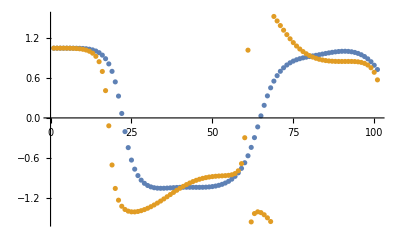

```mathematica
ListPlot[{ArcTan[Im[classSol]/Re[classSol]],ArcTan[Im[quantumSol]/Re[quantumSol]]} ]
```

```mathematica
Animate[ListPlot[{Labeled[Style[{Re[classSol[[i]]], Im[classSol[[i]]]}, Blue], "Classical"],Labeled[Style[{Re[quantumSol[[i]]], Im[quantumSol[[i]]]}, Red], "Quantum"]},PlotRange->{{-3, 3}, {-3,3}}], {i, 1, Length[classSol], 1}]
```

### Input state |001>

```mathematica
(* Set up parameters for solvers *)
params = {J->1,Γ->1, h1->1,h2->0,h3->0};
initAngles = {Subscript[θ, 1][0]==0,Subscript[θ, 2][0]==0,Subscript[θ, 3][0]==π};
initState = KroneckerProduct[{1, 0}, {1, 0}, {0, 1}]//Flatten;
tf = 10;
(* Actually solve in both cases *)
classSol = solveClassical[params,initAngles,tf];
quantumSol = solveQuantum[params,initState,tf];
```

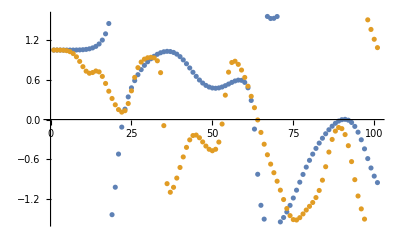

```mathematica
ListPlot[{ArcTan[Im[classSol]/Re[classSol]],ArcTan[Im[quantumSol]/Re[quantumSol]]} ]
```

```mathematica
Animate[ListPlot[{Labeled[Style[{Re[classSol[[i]]], Im[classSol[[i]]]}, Blue], "Classical"],Labeled[Style[{Re[quantumSol[[i]]], Im[quantumSol[[i]]]}, Red], "Quantum"]},PlotRange->{{-3, 3}, {-3,3}}], {i, 1, Length[classSol], 1}]
```